# Report Project 1

Course code: IX1500
Date: 2017-09-13

Task 1a: Poker Probability by census method

## Summary

### Task

The first task is to calculate the exact probability of the following hands in a variation of a poker game:

one pair

two pairs

three of a kind

four of a kind

five of a kind

full hand

straight

flush

straight flush

nothing

To calculate the exact probability  we will be using the census method.
The poker game consists of the cards 8,9,10,J,Q,K,A from two decks to construct sets of five playing cards. If one of the hand does contain more than one rank then the highest rank is considered e.g. if we want to calculate the probability of three of a kind and one of hands contains one pair, two pairs, three of a kind and full hand then the highest rank (full hand) is considered.

### Result

We have constructed below a table which shows the probability for each poker rank, from the lowest to the highest rank.

Hand | Probability | Probability,%
One pair | 11920/22737 | 52.426
Two pair | 1305/7579 | 17.219
Three of a kind | 2240/22737 | 9.852
Four of a kind | 140/22737 | 0.616
Five of a kind | 7/68211 | 0.01
Full hand | 392/22737 | 1.724
Straight | 1360/53053 | 2.563
Flush | 953/477477 | 0.200
Straight flush | 16/159159 | 0.01
Nothing | 8160/53053 | 15.381

## Calculating poker Probability by census method

By using the census method we can estimate the exact probability of each rank in a poker game.
   (|a|)/(|h|)= probability of a in h

 |a| is the amount of possibilites you can get on the total amount |h| 
 

First we construct the 5 cards 8,9,10,J,Q,K,A with their respective colors. Every card has 4 distinct colors (Red,  Black, Green, Blue), which means that we have to separate them by distinct numbers. This is the the result we get for one deck:

{{108,109,110,111,112,113,114},
{208,209,210,211,212,213,214},
{308,309,310,311,312,313,314},
{408,409,410,411,412,413,414}}

We represent the hundreds digit as the color and the two last sub values as the cards value, e.g. the card 108 has the color Red and has the card value 8 while the card 208 has the same card value but not the same color.

We construct another identical deck and join it with the first deck to get a every value we need from the two deck in one set:

{108,108,109,109,110,110,111,111,112,112,113,113,114,114,
208,208,209,209,210,210,211,211,212,212,213,213,214,214,
308,308,309,309,310,310,311,311,312,312,313,313,314,314,
408,408,409,409,410,410,411,411,412,412,413,413,414,414}

We also sorted the set above in numerical order to calculate the probability for each rank without adding extra condition to each calculation.

The last step is to generate all possible hands with five card in each hand:

{{108,108,109,109,110},
{108,108,109,109,110},
«3819813»,
{412,413,413,414,414}}
   
 The total possible hands we can get is 3 819 816.

### One pair

To calculate the probability for getting lowest rank one pair, we constructed a function called pairQ to sum up all generated hands which contains one pair. We excluded all the colors from every card to check if the two cards are identical.
We also excluded all the hands which contains; two pairs, three of a kind and flush, because we want to filter out every rank higher than one pair. There are even higher ranked poker hands which we want to filter out but we don’t need to because our filtered ranks already covers the higher ranks, e.g. one of a kind filters also four and five of a kind. The same principle is used when calculating the probability of almost every rank.   

The total amount of hands which only contains one pair is 2 002 560. 
By dividing the total number of hands containing one pair with the total possible hands we get the exact probability of one pair:

11920/22737≈ 52.426%

### Two pairs

The second lowest poker rank is two pair. We defined another function for two pairs and checked every possible hand by filtering out all hands which contains two pairs and doesn’t contain higher rank than our current rank.

The total amount of hands which only contains two pairs is 438 480. 
The total number of possibilities of two pairs divided by the total number of hands is the probability of the current rank:

1305/7579≈ 17.219%

### Three of a kind

We applied the same idea as in our two previous calculations when calculating the probability of getting three of a kind. Our new function threeKindQ filtered out four of a kind and full hand.

The total amount of hands which only contains three of a kind is 376 320 and the probability of the rank is:

2240/22737≈ 9.852%

### Four of a kind

To get the total amount of possible hands which contains four of a kind, we need to only filter out five of a kind.
The total amount of hands which only contains four of a kind is 23 520, and the probability of the rank is:

140/22737≈ 0.616%

### Five of a kind

Five of a kind contains 5 identical cards which doesn’t necessary need to have the same color. the rank is distinct to every other rank which makes it easier for us to get an answer because we don’t need to exclude any other rank.

The total amount of hands that contains only five of a kind is 392, and the probability of getting the rank is:

 7/68211≈ 0.01%

### Full hand

Full hand is the combination of 3 identical values followed by 2 different identical values, without taking colors into account. All ranks higher than full hand does not overlap the rank and we don’t need to filter anything out of our calculation.

By using the function fullHand, we get 65 856 amount of hand that contains the rank , and we get the probability:

 392/22737≈ 1.724%

### Straight

The rank straight is a bit different from previous ranks. We have to check if very hand has an ascending order where the first card is x and the second is x+1, the third is x+2, the fourth is x+3 and the last is x+4. By sorting every hand we can safely assume the lowest card value is always placed to the left of the hand and the highest to the right:
x_1 ≤ x_2 ≤ x_3 ≤ x_4 ≤ x_5 

flush[h]=h-h[[1]]=={0,1,2,3,4}

The function above takes the most left card and substitutes it with every card in the hand to check if it’s in ascending order from right to left.

The only thing we have to filter out of from our calculation is the highest rank straight flush. 
We can substitute the total all hands containing straight flush from our total amount of straight hands because every hand containing straight flush also contains the rank straight.
 
The answer we got is 98 304 amount of hands that contains straight and the probability of the rank is:

1360/53053≈ 2.563%

### Flush

The function “flush” is defined to a point where every card in a deck has to have the same color to be included in our total amount. We check if every cards hundred number is the same as the rest by dividing with 100. We also excluded every hand which contain the highest rank “straight flush” by substitution. 

The final answer we got is 8 008 possible hands which contains flush as the highest rank.
The probability of getting flush is:

953/477477≈ 0.2%

### Straight flush

To find every hand that contains straight flush we need to check if every all cards in each hand is in ascending order from left to right and we need to check if they all have the same color.
The function defined below checks if every card in the hand follows the ascending order from 0 to 4 by substituting every card by the first card, e.g. every card in the hand {108, 109, 110, 111, 112} gets substituted by 108 {(108 - 108), (109 - 108), (110 - 108), (111 - 108), (112- 108)}.
At the same time we are checking if the color is the same by not filtering the hundred number from every card.

straightFlush[h]=h-h[[1]]=={0,1,2,3,4}


 384 is the total amount of straight flush we got from all possible hands and the probability of it is:

16/159159≈ 0.1%

### Nothing

Calculating the probability nothing is pretty easy, we just have to exclude all hands which contains any kind of rank and count all hands with no rank.
We know that one pair filters out two pair, three, four, five of a kind and full hand, which is why only need one condition for the
 ranks. We also have to exclude flush and straight but not straight flush because it’s already filtered out.

 685 440 is total amount of hands with no rank and the probability of getting nothing is:

8160/53053≈ 15.381%

## Code

```mathematica
ClearAll["`*"]
```

```mathematica
(*Create distinct values ranging from 8 to A where A is 14*)
deck1 = Range[8,14];
deck = Table[deck1, {4}];

(*Add 4 colors to the deck *)
For[i=1,i<Length[deck]+1,i++, deck[[i]] = deck[[i]] + i*100   ];

(*This is 2 set of decks ranging from 8 to A*)
deck= Sort[Join[deck[[1]], deck[[1]],deck[[2]],deck[[2]],deck[[3]],deck[[3]], deck[[4]], deck[[4]]]] ;

(*Generate every possible hand*)
hands = Subsets[deck, {5}];
```

```mathematica
(**Straight flush**)
 (*Checks if current hand is in acsending order from left to right *)
straightFlush[h_]:=h-h[[1]]=={0,1,2,3,4};
(*Probability of straight flush*)
amountStraightFlush  = Count[hands, _? (straightFlush)] / Length[hands]
```

16/159159

```mathematica
(**Flush**)
(* Checks if all the cards have the same color *) 
flush[h_] := Equal@@ Quotient[h,100]; 
 (*Probability of flush*)
countFlush = (((Count[hands, _? (flush)])/ Length[hands]) -amountStraightFlush)
```

953/477477

```mathematica
(**Straight**)
 (*Checks if current hand is in acsending order from left to right *)
straight[h_] :=  MatchQ[h-h[[1]],{0,1,2,3,4}];
straights[v_] := straight[Sort[Mod[v,100]]]; 
(*Probability of straight*)
((Count[hands, _? (straights)])/ Length[hands]) -amountStraightFlush
```

1360/53053

```mathematica
(*Full hand*)
(* Get every hand which contains full hand*)
fullHand[{x_,x_,x_,y_, y_}/; x≠y]:= True; 
fullHand[{x_,x_,y_,y_, y_}/; x≠y]:= True; 
(* else *)
fullHand[_]:=False ; 
 (*Remove color from every card and sort every hand*)
fullHands[h_] := fullHand[Sort[Mod[h,100]]]; 
 (*Probability of full hand*) 
Count[hands, _? (fullHands)] / Length[hands]
```

392/22737

```mathematica
(**Five of a kind**)
(*we only need five of a kind*)
fiveKind[{x_,x_,x_,x_, x_}]:= True; 
 (* else *)
fiveKind[_]:=False ;
 (* Remove color from every card and sort all hands *)
fiveKinds[h_] := fiveKind[Sort[Mod[h,100]]];
(*Probability of five of a kind*)
Count[hands, _? (fiveKinds)] / Length[hands]
```

7/68211

```mathematica
(**Four of a kind**)
(* Filter out five of a kind *)
fourKind[{x_,x_,x_,x_, x_}]:= False;
(*We only need four of a kind*)
fourKind[{___,x_,x_,x_,x_,___}]:=True;
(*else *)
fourKind[_]:=False ; 
  (* Remove color from every card and sort all hands *)
fourKinds[h_] := fourKind[Sort[Mod[h,100]]];
(*Probability of four of a kind*)
Count[hands, _? (fourKinds)] / Length[hands]
```

140/22737

```mathematica
(**Three of a kind**)
 (* Filter out four of a kind *)
threeKindQ[{___,x_,x_,x_,x_,___}]:=False;
(* Filter out full hand *)
threeKindQ[{x_,x_,x_,y_,y_}/; x ≠ y] := False; 
(* Filter out full hand *)
threeKindQ[{x_,x_,y_,y_,y_}/; x ≠ y] := False;
(*We only need three of a kind *)
threeKindQ[{___,x_,x_,x_,___}]:=True; 
(* else *)
threeKindQ[{___}]:=False ; 
(* Remove color and sort all hands*)
threeKindQs[h_] := threeKindQ[Sort[Mod[h,100]]]; 
(*Probability of three of a kind*)
(Count[hands, _? (threeKindQs)])/ Length[hands]
```

2240/22737

```mathematica
(**Two pairs**)
(* Filter out three of a kind *)
twoPairQ[{___,x_,x_,x_, ___}]:=False; 
 (* We only need two pairs *)
twoPairQ[{___,x_,x_,___,y_,y_,___}/;x≠y]:=True;
(* else *)
twoPairQ[{___}]:=False ; 
(* Remove color, sort all hands and exclude flush *)
twoPairQs[h_] := twoPairQ[Sort[Mod[h,100]]]&&(!flush[h]); 
 (*Probability of of two pairs*)
(Count[hands, _? (twoPairQs)])/ Length[hands]
```

1305/7579

```mathematica
(**One pair**)
 (* Filter out two pairs *)
pairQ[{___,x_,x_,___,y_,y_,___}/;x≠y]:=False;
(* Exclude three of a kind *)
pairQ[{___,x_,x_,x_, ___}]:=False;
(* Only need a pair *)
pairQ[{___,x_,x_,___}]:=True;
(* else *) 
pairQ[{___}]:=False ; 
(* Exclude all colors from each card and sort all hands. Also exclude flush*)
pairQs[h_] := pairQ[Sort[Mod[h,100]]] &&(!flush[h]); 
(*Probability of one pair*)
(Count[hands, _? (pairQs)])/ Length[hands]
```

11920/22737

```mathematica
(**Nothing**)
(*Exclude one pair*)
nothing[{___,x_,x_,___}]:=False; 
(* else *)
nothing[{___}]:=True ;
(*Remove color and exclude flush and straight*)
nothings[h_] := nothing[Sort[Mod[h,100]]]&&(!flush[h])&&(!straights[h])
(Count[hands, _? (nothings)])/ Length[hands]
```

1360/7579

Task 1b: Poker Probability by combinatorial calculus

## Summary

### Task

The second task is to use combinatorial calculus to calculate the probability of flush, straight, full house, 3 of a kind and 4 of a kind. Every rank has to be compared to task 1a to check if the answers match.

### Result

The results is calculated by using combinatorial calculus which is also confirmed with the answer from task 1a.

Hand | Probability | Probability,%
Flush | 953/477477 | 0.1995907656
Straight | 1360/53053 | 2.563474262
Full house | 392/22737 | 1.724062101
3 of a kind | 2240/22737 | 9.851783437
4 of a kind | 140/22737 | 0.6157364648

## Using combinatorial calculus method to estimate the probability in Poker

### Flush

First we choose 5 cards from 14 cards with same color, there are 7 cards with same color in one deck ranging from 8 to A, with 2 decks we got 14 cards with same color. We have to choose 1 of 4 different colors. Finally we have to excluding the straight flush, where it has 3 possible straight from 8 cards ranging from 8 to A. The multiplication principle gives the result.
n_(different color)=Binomial[4, 1],n_(5cards)=Binomial[14, 5], n_(straight each color)=Binomial[3, 1], n_(1 card)=Binomial[8, 1]
n_(flush(incl. straight flush))=n_(different color)n_(5cards)=Binomial[4, 1] Binomial[14, 5]
Because there are 2 set of 4 different color which give a combination of square of 4 which is 16.
n_(straight flush)=n_(straight each color)n_(1card)=16Binomial[3, 1] Binomial[8, 1]
∴P_flush=(n_(flush -)n_(straight flush))/n_tot=(Binomial[4, 1] Binomial[14, 5]-16Binomial[3, 1] Binomial[8, 1])/Binomial[56, 5]=953/477477≈0.1995907656%

### Straight

There are 3 different ways to create straight for each deck of same color ranging from 8 to A. From the two sets of deck we can choose 1 of 8 cards, and we have to choose that 5 times. Due to the multiplication principle, it gives us 8 choose 1 elevated with 5. In the end we need to excluding the straight flush which is included in straight.

 n_(straight each color)=Binomial[3, 1], n_(one card of each value)=Binomial[8, 1]
n_straight=n_(straight each color),n_(one card of each value ^5)=Binomial[3, 1] Binomial[8, 1]^5
Just as mentioned before the straight flush need to be subtracted.
n_(straight flush)=n_(straight each color)n_(1card)=16Binomial[3, 1] Binomial[8, 1]
∴P_straight=n_straight/n_tot=(Binomial[3, 1] Binomial[8, 1]^5 -16 Binomial[3, 1]Binomial[8, 1])/Binomial[56, 5]=1360/53053≈2.56347426%

### Full house

First we choose one of seven possibilities to be kind value x, then we choose three out of the eight x. And same with the one pair value y, we choose one of six possibilities which is left after have choose three card of x. The multiplication principle gives the result.
 n_(one of seven cards)=Binomial[7, 1], n_(three card of same value)=Binomial[8, 3],  n_(one of six)=Binomial[6, 1], n_(two card of each value)=Binomial[8, 2]
n_(full house)=n_(one of seven cards)n_(three card of same value)n_(one of six)n_(two card of each value)=Binomial[7, 1]Binomial[8, 3]Binomial[6, 1] Binomial[8, 2]
∴P_(full house)=(n_(full house))/n_tot=(Binomial[7, 1] Binomial[8, 3] Binomial[6, 1]Binomial[8, 2])/Binomial[56, 5]=392/22737≈1.724062101%

### 3 of a kind

In order to find 3 kind, we choose one of seven possibilities of value x, we take three cards out of eight. Then we can just take randomly 2 cards out of 48 cards without value x. Secondly we need to subtract full house to get the right answer.
 n_(one of seven cards)=Binomial[7, 1], n_(three card of same value)=Binomial[8, 3],  n_(2 out of 48)=Binomial[48, 2]
n_(three kind)=n_(one of seven cards)n_(three card of same value)n_(2 out of 48)=Binomial[7, 1]Binomial[8, 3]Binomial[48, 2] 
∴P_(three kind)=(n_(three kind))/n_tot=(Binomial[7, 1] Binomial[8, 3] Binomial[48, 2] - full house(taking the value from earlier))/Binomial[56, 5]=2240/22737≈9.851783437%

### 4 of a kind

To calculate four kind we take one of seven possibilities and we can choose four of eight cards with same value. There are one card that we can choose out of 48 cards.
n_value=Binomial[7, 1],n_(4cards)=Binomial[8, 4], n_last=Binomial[48, 1]
n_4=n_value n_(4cards)n_last=Binomial[7, 1] Binomial[8, 4]Binomial[48, 1]
∴P_4=n_4/n_tot=(Binomial[7, 1] Binomial[8, 4]Binomial[48, 1])/Binomial[56, 5]=23520/3819816=140/22737≈0.615736%

## Code

Flush

```mathematica
flushBinom = (Binomial[14,5]*Binomial[4,1]-Binomial[3,1]*Binomial[8,1]*16)/Binomial[56,5]
```

953/477477

Straight

```mathematica
straightBinom  = (Binomial[3,1]*Binomial[8,1]^5-Binomial[3,1]*Binomial[8,1]*16)/Binomial[56,5]
```

1360/53053

Full house

```mathematica
fullHouseBinom = Binomial[7,1]*Binomial[8,3]*Binomial[6,1]*Binomial[8,2]/Binomial[56,5]
```

392/22737

3 of a kind

```mathematica
threeKindBinom = (Binomial[7,1]*Binomial[8,3]*Binomial[48,2]/Binomial[56,5]) - fullHouseBinom
```

2240/22737

4 of a kind

```mathematica
fourKindBinom  = Binomial[7,1]*Binomial[8,4]*Binomial[48,1]/Binomial[56,5]
```

140/22737

Task 1c: Poker Probability by Monte Carlo method

## Summary

### Task

In this task we are going to calculate the probability of getting one pair using the Monte Carlo method. We will also draw a diagram that shows how the probability estimate stabilises with increasing sample size. This task will also be compared to task 1a to check if our approximate answer is close to the exact answer.

### Result

Using Monte Carlo method to estimate the probability of getting one pair after 3000 games. We came up with a probability of 53.133 % after 3000 hands/games. Each game is defined as one hand with 5 cards each hand. The result from estimation of Monte Carlo can compare with the result from task 1 which is 52.426 %.

## Calculating probability of one pair using Monte Carlo

### Solution to calculate one pair

We start with randomly choosing 5 cards from the decks which represent as a randomly hand.
Secondly we work numerically starting by multiplying the randomly hand with 100 up to 3000 times, which represent the amount of hand. For each hand which is a pair will count as true and false otherwise using the code from task 1. And for every true is counted as 1 and false 0. 

We count all the trues and dividing it by the amount of hands we created which gives the probability of one pair using Monte Carlo. We can observe that the result is varying a lot ranging 1 to 500 hands/games. The result quickly stabilize and converge after 500 games and even more after 1000 games that as we can see in the diagram below.

Games,# | Probability,%
100 | 57
200 | 53.212
300 | 53
400
500
600
700
800
900
1000
1500
2000
2500
3000 | 49.752
48.8
56.333
50.571
50
55.223
51.721
52.273
52
51.447
53.133

The table above demonstration the probability with the responding amount of games.

The amount of games is determined to be 3000 games in this case.The reason is that in the diagram below,we can see the probability begin to converge after a few hundred of games and the line is varying much less after 2000 games comparing to the beginning. The principle is that with more data,the method gives more confidence in it's result.

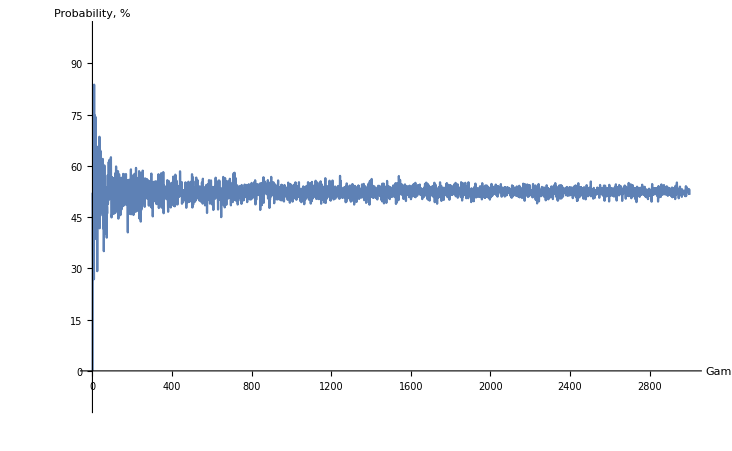

The diagram above illustrate the probability of getting one pair using Monte Carlo method with increasing games/hands.

## Code

We are using the deck and randomly select 5 cards which represent a play or a hand.

```mathematica
Clear[play]
play := Sort/@Partition[RandomSample[deck, 1*5], 5]
```

Create the function omega3 where the parameter is used to multiply the play

```mathematica
Clear[omega3]
omega3[n_] := Table[play, {n}];
```

Example, creating a table with n = 2000, which says the function creates 2000 plays or hands.

```mathematica
n = 2000;
omega3[n_] := Table[play, {n}];  
omega3[n]
```

{{{108,109,111,212,410}},{{112,211,211,311,409}},1997,{{108,109,312,411,413}}}
 |  |  |  |

Function p3 is calculating the probability of one pair from random selected hands.

```mathematica
pair3[play_] := Or@@pairQs/@play
p3[n_] := (Count[omega3[n], _?(pair3)]*100)/(n);
```

Plot is used in order to create a diagram which illustrates the probability with increasing games/hands.

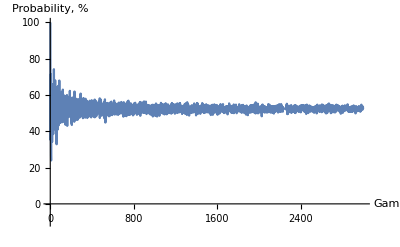

```mathematica
Plot[p3[n],{n,1,3000}, AxesLabel->{"Game", "Probability, %"}, PlotRange->{-0.1*100,1*100}]
```